This simply outlines the derivation for the "classic" case with only CP cells (A) and no counting generations. The basic starting point is the master equation:

∂_t P_m[t]==λ ((m-1) r P_(m-1)[t]+(m+1) r P_m[t]+m (1-2 r) P_m[t]-m P_m[t])

We can transform to a generating function:

F[x,t]==∑_(m=0)^∞ x^m P_m[t]

Noting that we have natural boundary conditions P_m=0 for m<0 we have that:

m x^m==x ∂_x x^m

Thus we can write the master equation as a PDE for the generating function F :

∂_t F[x,t]==λ r (1-x)^2 ∂_x F[x,t]

Which we can solve, with the initial conditions P_m=δ_(m,1):

```mathematica
DSolve[{D[F[x,t], t]==λ r (1-x)^2 D[F[x,t], x], F[x,0] == x}, F,{x,t}]
Subscript[P, m_][t_] := Evaluate[SeriesCoefficient[F[x,t] /. %[[1]], {x,0,m}]]
Subscript[P, m][t]
```

{{F→Function[{x,t},(-x-r t λ+r t x λ)/(-1-r t λ+r t x λ)]}}

Piecewise[{{((r t λ)/(1+r t λ))^(-1+m)/(1+r t λ)^2, m≥1}, {-((r t λ)/(1+r t λ))^m/(1+r t λ), 0<m<1}, {1-1/(1+r t λ), m==0}, {0, True}}]

We find a nice scaling relationship for the persisting clones:

```mathematica
Limit[(m Subscript[P, m][t m])/(1-Subscript[P, 0][t m]), m->∞]
```

ⅇ^(-1/(r t λ))/(r t λ)

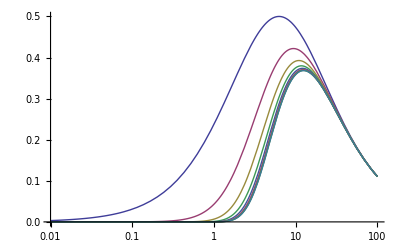

```mathematica
LogLinearPlot[Evaluate[Table[(m Subscript[P, m][t m])/(1-Subscript[P, 0][t m])/.{m->2^n,λ->1.0,r->0.08},{n,1,9}]],{t,0.01,100},PlotRange->All,AxesLabel->{t/m}]
```

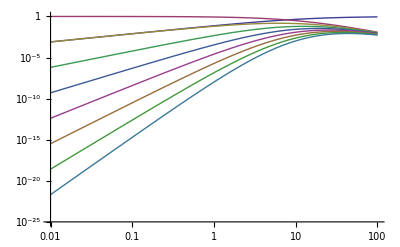

```mathematica
LogLogPlot[Evaluate[Table[Tooltip[Subscript[P, m][t ],m]/.{m->n,λ->1.0,r->0.08},{n,0,8}]], {t, 0.01, 100},PlotRange->{10^-25,1},AxesLabel->{t}]
```